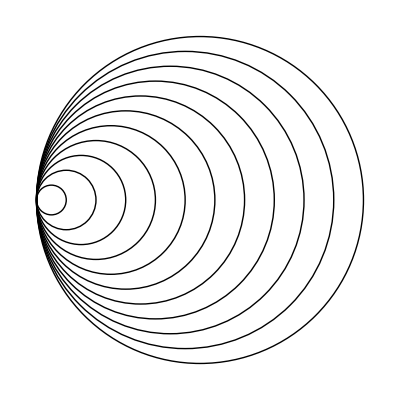

```mathematica
(*Practicando con Graficos*)
(*Poner Graphics antes que Table, hace un grafico combinando las listas.
Hacelo a la inversa, creara una lista con cada elemento siendo un grafico*)
Graphics@Table[Circle[{x,0},x],{x,11}]
```

```mathematica
(*Notece que es un grafico al final de cuentas*)
```

```mathematica
Graphics@Table[Circle[RandomInteger[30,2],RandomInteger[10]],90]
```

-Graphics-

```mathematica
(*Se hicieron 90 circulos con posicion aleatoria, producto de la lista RandomInteger[30,2],la cual emtrega 2 elementos con un rango de aleatoriedad de 30; RandomInteger[10], es el radio del circulo*)
(*Se usa el mismo concepto que en:*)
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Que repite 10 veces lo que se encuentre en el elemento*)
```

```mathematica
(*Entrando a 3D, en wolfram, la x aumenta hacia la derecha, la 'y' se mete dentro de la pantalla y 'z' aumenta de abajo hacia arriba*)
Graphics3D[{Sphere[{0,0,0}],Sphere[{0,0,2}]}]
```

-Graphics3D-

```mathematica
(*Usando Manipulate*)
```